```mathematica
(*This is a Wolfram Mathematica v.11 notebook file.
For more info, see the following GitHub repository:
https://github.com/TMS-Namespace/Critical-Phenomena-in-Gravitational-Collapse
*)
(*-------------Loading data from relative location*)
```

```mathematica
LoadData[FileName_]:=Import[FileNameJoin[{NotebookDirectory[],"Simulation Results",FileName<>".cvs"}]];
```

```mathematica
(*-------------Parameters used for simulation*)
```

```mathematica
GridSize=4000;Step=0.0025;Gap=20;DrawingPoints=GridSize/Gap;
```

```mathematica
(*------------- becuase the output is half of the grid, we need to calc how much recoreds in each slice*)
```

```mathematica
GetVShift[u_]:=Sum[DrawingPoints-n+1,{n,1,u}]+1;
```

```mathematica
(*-------------This will plot UCount slices of the 3D grid starting from UShift slice*)
```

```mathematica
PlotUSlices[Arr_,UShift_,UCount_:1,YAxisLabel_:"",Title_:"",YRange_:{"",""}]:=Module[
{Shift=GetVShift[UShift],fNaN,Tab,Leg,Ser,uVal,vVal},

vVal[v_]:=v*Step;

If[GetVShift[UShift+UCount-1+1]-1>=Length[Arr]-1,Return["Exeeded Max Length"]];

Ser[u_]:=Table[{vVal[Arr[[n]][[2]]],Arr[[n]][[3]]},{n,GetVShift[UShift+u],GetVShift[UShift+u+1]-1}];

Tab=Table[Ser[u],{u,0,UCount-1}];

uVal[u_]:=(UShift+u)*GridSize/DrawingPoints*Step;

Leg=Table["u="<>ToString[uVal[u]],{u,UCount}];

ListLinePlot[Tab,PlotLegends->Leg,AxesLabel->{Style["v",Blue,FontSize->13,FontWeight->Bold],
		   Style[YAxisLabel,Purple,FontSize->13,FontWeight->Bold]},
PlotLabel->Style[Title,Bold,16],
PlotRange-> If[YRange[[1]]=="",Full,{{0,10},YRange}],AspectRatio->1/2]
]
```

```mathematica
(*------------- This will Plot full 3D grid*)
```

```mathematica
PlotFull[Arr_,ZLabel_,Title_:"",ZRange_:{"",""}]:=Module[
{fNaN,Tab,Val},

Val[x_]:=x*Step;

Tab=
Table[{Val[Arr[[n]][[2]]],Val[Arr[[n]][[1]]],Arr[[n]][[3]]},{n,Length[Arr]-1}];

ListPlot3D[Tab,
AxesLabel->{Style["v",Blue,FontSize->13,FontWeight->Bold],
		   Style["u",Red,FontSize->13,FontWeight->Bold],
		   Style[ZLabel,Purple,FontSize->13,FontWeight->Bold]},
PlotLabel->Style[Title,Bold,16],
PlotRange-> If[ZRange[[1]]=="",Full,{{0,10},{0,10},ZRange}]]
]
```

```mathematica
(*-------------This will plot Mass with linear fitting, one can crop the data from left and right to avoid spikes*)
```

```mathematica
Critical[LgMLgA_,CropD_:0,CropU_:0]:=Module[
{CropLgMLgA,FitM,xU,xD,yU,yD,Fitted,OrgPlot,FittedPlot,P,Y},

CropLgMLgA=Table[{LgMLgA[[n]][[3]],LgMLgA[[n]][[4]]},{n,1+CropD,Length[LgMLgA]-CropU}];

FitM=LinearModelFit[CropLgMLgA,x,x];

xD=CropLgMLgA[[1]][[1]];
xU=CropLgMLgA[[Length[CropLgMLgA]]][[1]];
Y=Table[CropLgMLgA[[n]][[2]],{n,1,Length[CropLgMLgA]}];yD=Min[Y];
yU=Max[Y];

OrgPlot=ListPlot[CropLgMLgA,
AxesLabel->{Style[ln[Subscript[M, BH]],Blue,FontSize->13,FontWeight->Bold],
Style[ln[A-SuperStar[A]],Purple,FontSize->13,FontWeight->Bold]},
PlotRange->{{xD,xU},{yD,yU}},
PlotMarkers->{Automatic,9}];

FittedPlot=Plot[FitM[x],{x,xD,xU},PlotLabel->Normal[FitM],PlotStyle->Red,
PlotRange->{{xD,xU},{yD,yU}},
PlotLegends->Placed[Normal[FitM],{{0.5,0},{1,-1}}]];

Show[{OrgPlot,FittedPlot}]
]
```

```mathematica
(*======Vacuum============================================*)
```

```mathematica
aVacuum=LoadData["a_Vacuum"];
```

```mathematica
TitleVacuum="Vacuum";
```

```mathematica
PlotFull[aVacuum,"a",TitleVacuum]
```

-Graphics3D-

```mathematica
ErrorVacuum=LoadData["Error_Vacuum"];
```

```mathematica
PlotFull[ErrorVacuum,"Error",TitleVacuum,{-0.1,0.1}]
```

-Graphics3D-

```mathematica
(*======SuB critical============================================*)
```

```mathematica
TitleSub="A≲A^*";
```

```mathematica
rSub=LoadData["r_SuB"];
```

```mathematica
PlotFull[rSub,"r",TitleSub]
```

-Graphics3D-

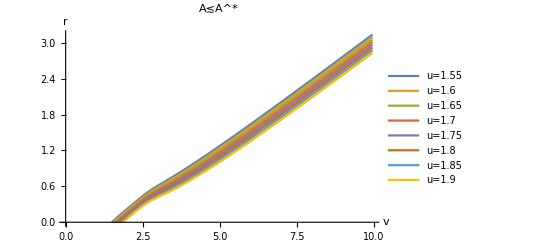

```mathematica
PlotUSlices[rSub,30,8,"r",TitleSub,""]
```

```mathematica
RvSub=LoadData["Rv_SuB"];
```

```mathematica
PlotFull[RvSub,"Rv",TitleSub]
```

-Graphics3D-

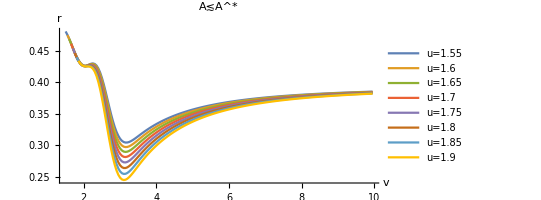

```mathematica
PlotUSlices[RvSub,30,8,"r",TitleSub]
```

```mathematica
PhiSub=LoadData["Phi_SuB"];
```

```mathematica
PlotFull[PhiSub,"Φ",TitleSub]
```

-Graphics3D-

```mathematica
aSub=LoadData["a_SuB"];
```

```mathematica
PlotFull[aSub,"a",TitleSub]
```

-Graphics3D-

```mathematica
ErrorSub=LoadData["Error_SuB"];
```

```mathematica
PlotFull[ErrorSub,"Error",TitleSub]
```

-Graphics3D-

```mathematica
(*======SuPer critical============================================*)
```

```mathematica
TitleSup="A≳A^*";
```

```mathematica
rSup=LoadData["r_SuP"];
```

```mathematica
PlotFull[rSup,"r",TitleSup,{-1,5}]
```

-Graphics3D-

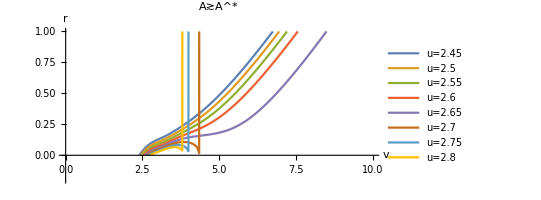

```mathematica
PlotUSlices[rSup,48,8,"r",TitleSup,{-0.2,1}]
```

```mathematica
RvSup=LoadData["Rv_Sup"];
```

```mathematica
PlotFull[RvSup,"Rv",TitleSup,{-0.2,0.6}]
```

-Graphics3D-

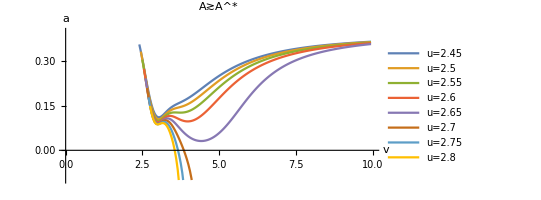

```mathematica
PlotUSlices[RvSup,48,8,"a",TitleSup,{-0.1,0.4}]
```

```mathematica
PhiSup=LoadData["Phi_SuP"];
```

```mathematica
PlotFull[PhiSup,"Φ",TitleSup,{-2.5,1.2}]
```

-Graphics3D-

```mathematica
aSup=LoadData["a_Sup"];
```

```mathematica
PlotFull[aSup,"a",TitleSup,{-0.1,1.8}]
```

-Graphics3D-

```mathematica
ErrorSup=LoadData["Error_SuP"];
```

```mathematica
PlotFull[ErrorSup,"Error",TitleSup,{-0.005,0.03}]
```

-Graphics3D-

```mathematica
v=3500;
```

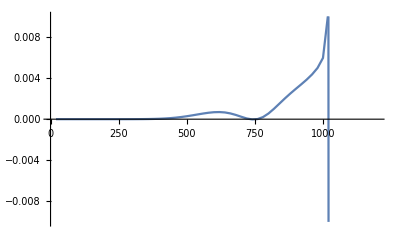

```mathematica
ListLinePlot[Table[{u*20,ErrorSup[[GetVShift[u]+v/Gap-(u-1)]][[3]]},{u,v/Gap}],PlotRange->{{0,1200},{-0.01,0.01}}]
```

```mathematica
(*======Critical Phenomena=======================================*)
```

```mathematica
LnTPhiSub=LoadData["LnT_Phi_Sub"];
```

```mathematica
LnTPhiSup=LoadData["LnT_Phi_Sup"];
```

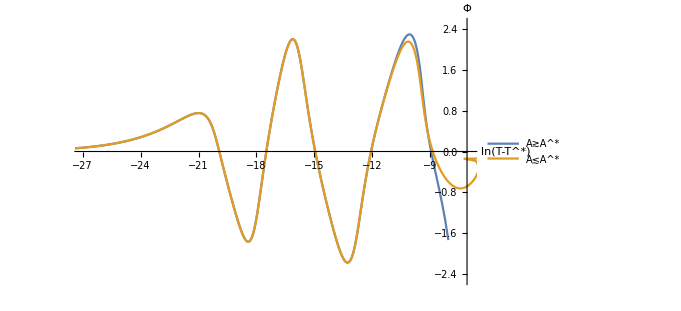

```mathematica
ListLinePlot[{LnTPhiSup,LnTPhiSub},PlotRange->{{-27,-7},{-2.5,2.5}},PlotLegends->Placed[{TitleSup,TitleSub},{{0.3,0.6},{1.3,-1}}],AxesLabel->{Style[ln[T-SuperStar[T]],Blue,FontSize->13,FontWeight->Bold],
		   Style[Φ,Purple,FontSize->13,FontWeight->Bold]}]
```

```mathematica
(16.12-10.13)
```

5.99

```mathematica
*N[Log10[Exp[1]]]
```

```mathematica
(*-------------*)
```

```mathematica
LnTLnaSuB=LoadData["LnT_Lna_SuB"];
```

```mathematica
LnTLnaSuP=LoadData["LnT_Lna_SuP"];
```

```mathematica
ListLinePlot[{LgTLgaSuP,LgTLgaSuB},PlotRange->{{-20,-7},{-5,0}},PlotLegends->Placed[{TitleSup,TitleSub},{{0.5,0},{1,-1}}],AxesLabel->{Style[ln[T-SuperStar[T]],Blue,FontSize->13,FontWeight->Bold],
		   Style[ln[a],Purple,FontSize->13,FontWeight->Bold]}]
```

-Graphics-

```mathematica
(*-------------*)
```

```mathematica
LnMLnA=LoadData["LnA_LnM"];
```

```mathematica
Critical[LnMLnA,2,5]
```

-Graphics-

```mathematica
(*-------------*)
```

```mathematica
LnTLnRSub=LoadData["LnT_LnR_Sub"];
LnTLnRSup=LoadData["LnT_LnR_Sup"];
```

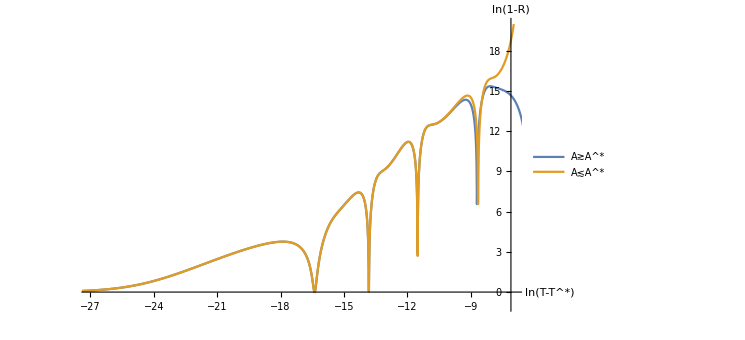

```mathematica
ListLinePlot[{LnTLnRSub,LnTLnRSup},PlotRange->{{-27,-7},{-1,20}},AxesLabel->{Style[ln[T-SuperStar[T]],Blue,FontSize->13,FontWeight->Bold],
		   Style[ln[1-R],Purple,FontSize->13,FontWeight->Bold]},
PlotLegends->Placed[{TitleSup,TitleSub},{{0.3,0.4},{1.3,-1}}]]
```